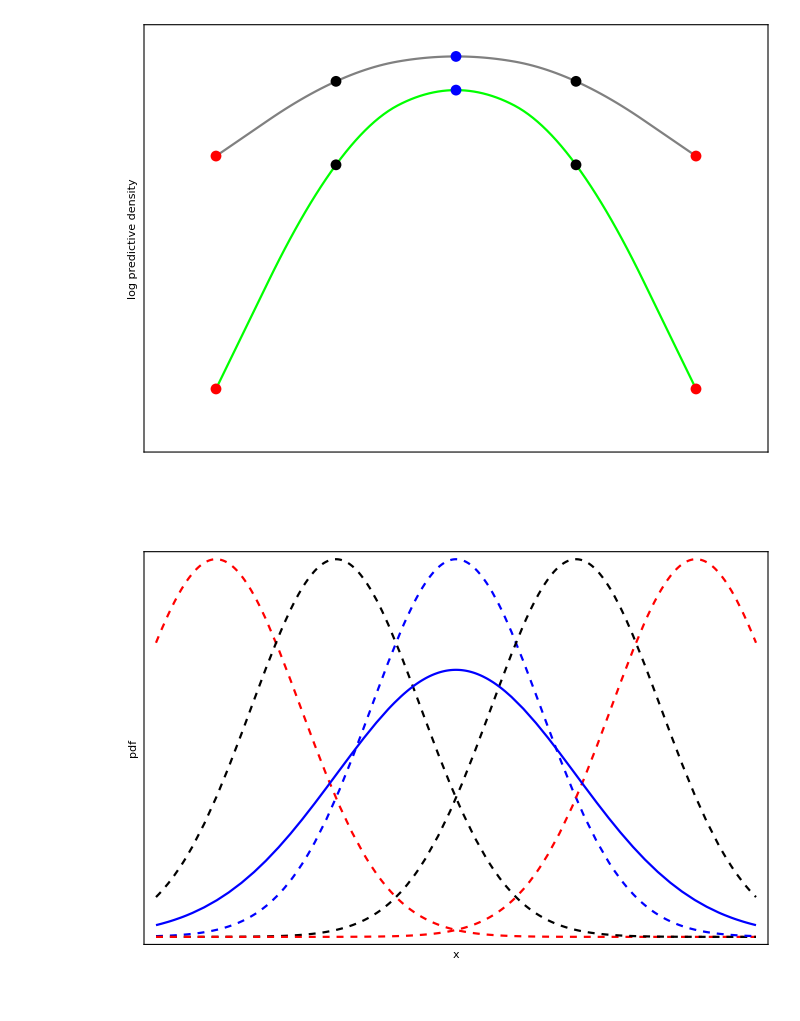

```mathematica
SetDirectory[NotebookDirectory[]];
ClearAll["Global`*"]
felpd1[aDist_,aDist1_]:=Module[{x},Expectation[N@Log[PDF[aDist,x]],x\[Distributed]aDist1]]
n = 1;
σ1 = 2;
trueDist = NormalDistribution[5,σ1];
data = RandomVariate[trueDist,{n}];
xbar = Mean@data;
μ0 = 5;
σ0 = 2;
fPosteriorPredictive[x_,aPosteriorDist_]:=Integrate[Likelihood[NormalDistribution[μ,σ1],{x}] * PDF[aPosteriorDist,μ],{μ,-20,20}]
fGetlppd[x_]:=Module[{aDatum=Solve[((μ0/(σ0^2)) + (n y)/(σ1^2)) / ((1/(σ0^2))+ (n/(σ1^2)))==x,y][[1,1,2]],aPosteriorDist},aPosteriorDist = NormalDistribution[((μ0/(σ0^2)) + (n aDatum)/(σ1^2)) / ((1/(σ0^2))+ (n/(σ1^2))), Sqrt[((1/(σ0^2))+ (n/(σ1^2)))^(-1)]];n*N@Log@fPosteriorPredictive[aDatum,aPosteriorDist]]
fGetelpd[x_,aTrueDist_]:=Module[{aDatum=Solve[((μ0/(σ0^2)) + (n y)/(σ1^2)) / ((1/(σ0^2))+ (n/(σ1^2)))==x,y][[1,1,2]],aPosteriorDist},aPosteriorDist = NormalDistribution[((μ0/(σ0^2)) + (n aDatum)/(σ1^2)) / ((1/(σ0^2))+ (n/(σ1^2))), Sqrt[((1/(σ0^2))+ (n/(σ1^2)))^(-1)]]; felpd1[aPosteriorDist,aTrueDist]]
fGetPosterior[x_,aTrueDist_]:=Module[{aDatum=Solve[((μ0/(σ0^2)) + (n y)/(σ1^2)) / ((1/(σ0^2))+ (n/(σ1^2)))==x,y][[1,1,2]],aPosteriorDist},aPosteriorDist = NormalDistribution[((μ0/(σ0^2)) + (n aDatum)/(σ1^2)) / ((1/(σ0^2))+ (n/(σ1^2))), Sqrt[((1/(σ0^2))+ (n/(σ1^2)))^(-1)]]]
alpd=ParallelTable[{x,fGetlppd[x]},{x,1,9,2}];
aelpd=ParallelTable[{x,fGetelpd[x,trueDist]},{x,1,9,2}];
cList=Table[PDF[fGetPosterior[x,trueDist],y],{x,1,9,2}];
{yMin,yMax}  = {-7,-1.5};
g1=Show[ListLinePlot[{alpd,aelpd},PlotRange->{{0,10},{yMin,yMax}},InterpolationOrder->2,PlotStyle->{Gray,Green},Frame->{True,True,False,False},FrameTicks->{None,None},FrameLabel->{"","log predictive density"},BaseStyle->{FontSize->16}],ListPlot[{alpd[[1]],aelpd[[1]]},PlotRange->{{0,10},{yMin,yMax}},PlotStyle->Red,Frame->{True,True,False,False},FrameTicks->{None,None},FrameLabel->{"","elpd"},BaseStyle->{FontSize->16}],ListPlot[{alpd[[2]],aelpd[[2]]},PlotRange->{{0,10},Full},PlotStyle->Black],ListPlot[{alpd[[3]],aelpd[[3]]},PlotRange->{{0,10},Full},PlotStyle->Blue],ListPlot[{alpd[[4]],aelpd[[4]]},PlotRange->{{0,10},Full},PlotStyle->Black],ListPlot[{alpd[[5]],aelpd[[5]]},PlotRange->{{0,10},Full},PlotStyle->Red]];
g2=Show[Plot[cList,{y,0,10},PlotStyle->{{Dashed,Red},{Dashed,Black},{Dashed,Blue},{Dashed,Black},{Dashed,Red}},Frame->{True,True,False,False},FrameTicks->{None,None},FrameLabel->{"x","pdf"},BaseStyle->{FontSize->16}],Plot[PDF[trueDist,x],{x,0,10},PlotStyle->Blue]];
gFinal=Show[GraphicsColumn[{g1,g2}],ImageSize->800]
```

```mathematica
Export["Evaluation_lppdOverconfidence.pdf",gFinal]
```

Evaluation_lppdOverconfidence.pdf